# Initial Plotting Experiments

```mathematica
Plot[{Exp[-x], Cos[2x], Log[x]}, {x,0,5}, 
PlotStyle->{{Blue},{Green, Dashing[0.01]},{Orange,Dashing[0.019]}},
Frame-> True,PlotLabel->Style["Assignment 2",Italic,Underlined,15],PlotLegends ->"Expressions"]
```

-Graphics-

# Quadratic Behaviors

```mathematica
Manipulate[Plot[{a x^(2)+b x+c, -a x^(2)+c}, {x,-100,100},
PlotRange->{{-10,10},{-10,10}},Frame->True,
PlotLabel->Style["Quadratic Functions and Their Minimas",Italic,Underlined,15]], 
    {a,-5,5},{b,-5,5},{c,-5,5}]
```

```mathematica
Plot[{-Cos[x],-Sin[x]/x,(-1/x)+(1/x^2)},{x,-2Pi,2Pi},
PlotLegends->"Expressions",PlotStyle->Thick,
PlotRange->{-5,5},Frame->True]
```

-Graphics-

```mathematica
Plot[{-Sin[x]/x,-1+x^(2)/6},{x,-2π,2π}]
```

-Graphics-

```mathematica
Plot[{(-1/x)+(1/x^2),(1/16)(x-2)^(2)-(1/4)},{x,1.999,2.001}]
```

-Graphics-

```mathematica
0
```

0

```mathematica
Manipulate[Plot[{x^(1/n),Log[x]},{x,15,15.5},PlotRange->{-10,10}PlotLegends->"Expressions"],{n,0,100}]
```

General::prng: Value of option PlotRange -> {-10 PlotLegends,10 PlotLegends}→Expressions is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 15.^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 15.0102^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 15.0204^ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Plot[{Exp[-x^2],1/(x^(2)+1),1-x^(2)},{x,-3,3},PlotLegends->"Expressions",PlotStyle->{{Orange,Thickness[0.006],Dashing[Infinity]},{Blue,Thickness[0.004],Dashing[0.03]},{Magenta,Thickness[0.005],Dotted}},PlotRange->{0,1}]
(*lorentzian function is a long range function because it has a long tail, and Gaussian is a short range function.*)
```

-Graphics-

```mathematica
Manipulate[Plot[{Sech[x],1-(x^(2)/2)},{x,-3,3},PlotRange->{-1.2,1.2}],{a,-5,5,1}]
```

```mathematica
Series[Sech[x],{x,0,2}]
```

1-x^2/2+O[x]^3

```mathematica
Plot[{Sech[x],1/(x^(2)+1),Exp[-x^(2)]},{x,-10,10},PlotRange->{0,0.1},PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
Plot[{x^(2)/2,1-Cos[x]},{x,0,1},PlotRange->{0,1}]
```

-Graphics-

```mathematica
Manipulate[Plot[{-(k x^(2)/(Cos[y])^(2))+x Tan[y]+1,-(x Tan[ø])+1},{x,0,1},PlotRange->{0,1}],{k,0,1000000},{ø,0,2π},{y,0,2π}]
```

```mathematica
ParametricPlot[{x Cos[x],x Sin[x]},{x,0,20},AxesLabel->{"X","Y"},PlotLabel->Style["Parametric Plot",Italic,Underlined,15]]
```

-Graphics-

# Vector Plots and Stream Plots

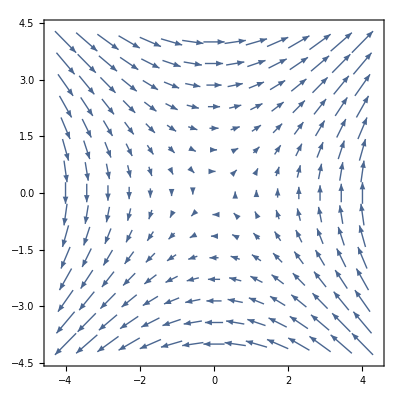

```mathematica
vectorplot1 = VectorPlot[{y,x}, {x, -4, 4}, {y, -4,4}]
```

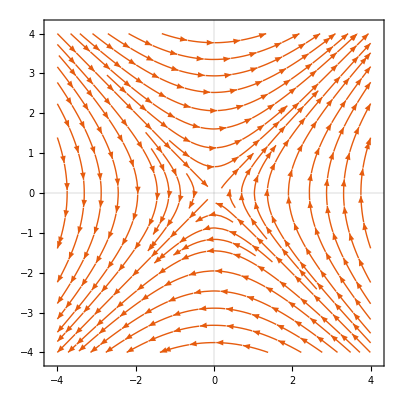

```mathematica
Streamplot1 = StreamPlot[{y,x}, {x, -4, 4}, {y, -4,4},RegionFunction->Function[{x,y,vx,vy,n},(x^2)+(y^2)>0.05],PlotTheme->"Scientific"]
```

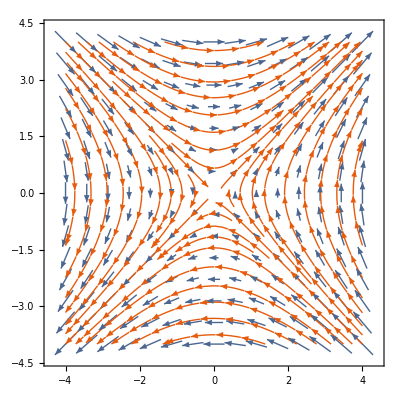

```mathematica
Show[vectorplot1,Streamplot1]
```

# Electric Dipole

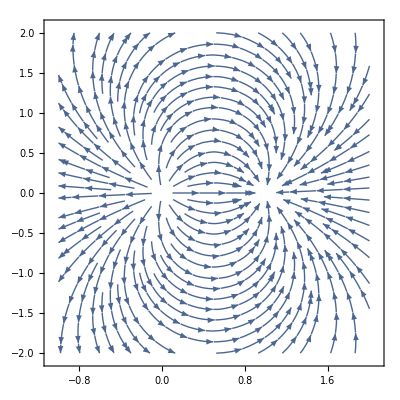

```mathematica
fieldlines=StreamPlot[{((x)/(r^3))-((x-1)/(r1^3)),((y)/(r^3))-((y)/(r1^3))}
/.r->(((x^2)+(y^2))^(0.5))/.r1->((((x-1)^2)+(y^2))^(0.5)),{x,-1,2},{y,-2,2},RegionFunction->Function[{x,y},((x^2)+(y^2))≥0.01&&(((x-1)^2)+(y^2))≥0.01]]
```

```mathematica
potential=ContourPlot[{(1/(r))-(1/(r1))}/.r->(((x^2)+(y^2))^(0.5))/.r1->((((x-1)^2)+(y^2))^(0.5)),{x,-1,2},{y,-2,2}]
```

-Graphics-

```mathematica
Show[potential,fieldlines]
```

-Graphics-

```mathematica
Plot[{2Sin[2t]+Cos[2t],2Cos[2t+(π/4)],2Sin[2t+(π/4)]},{t,-2π,2π},PlotLegends->"Expressions",Frame->True,FrameLabel->{"x","t"}]
```

-Graphics-

# Quadripole

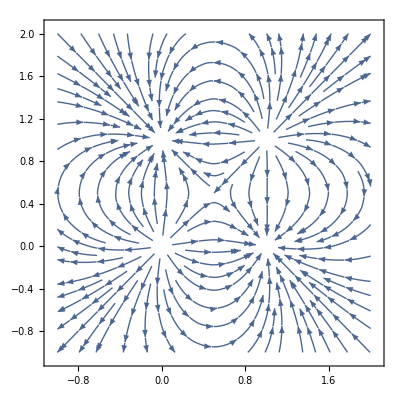

-Graphics-

```mathematica
quadripolefield=StreamPlot[{(x/r^3)-((x-1)/r1^3)-(x/r2^3)+((x-1)/r3^3),
(y/r^3)-(y/r1^3)-((y-1)/r2^3)+((y-1)/r3^3)} 
   /.r->(((x^2)+(y^2))^(0.5))/.r1->((((x-1)^2)+(y^2))^(0.5))
   /.r2->(((x^2)+((y-1)^2))^(0.5))/.r3->((((x-1)^2)+((y-1)^2))^(0.5)),
   {x,-1,2},{y,-1,2},RegionFunction->Function[{x,y},
((x^2)+(y^2))≥0.01&&(((x-1)^2)+(y^2))≥0.01&&
((x^2)+((y-1)^2))≥0.01&&(((x-1)^2)+((y-1)^2))≥0.01]]
quadripolepotential=ContourPlot[{(1/r)-(1/r1)-(1/r2)+(1/r3)}
/.r->(((x^2)+(y^2))^(0.5))/.r1->((((x-1)^2)+(y^2))^(0.5))
 /.r2->(((x^2)+((y-1)^2))^(0.5))/.r3->((((x-1)^2)+((y-1)^2))^(0.5)),
 {x,-4,4},{y,-4,4}]
 Show[quadripolepotential,quadripolefield];
```

# Magnetic Dipole

```mathematica
StreamPlot[{(3x z)/r1^3,((3(z)^2)-1)/r1^3}
   /.r1->(((x^2)+(z^2))^(0.5)),{x,-2,2},{z,-2,2},
    RegionFunction->Function[{x,z},((x^2)+((z-0.5)^2))≥0.03
&&((x^2)+((z+0.5)^2))≥0.03]]
```

-Graphics-

# Two Parallel Wires Carrying Electric Current

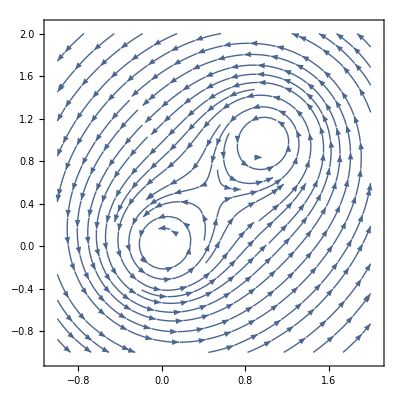

```mathematica
StreamPlot[{(-y/(r1^2))-((y-1)/(r2^2)),(x/(r1^2))+((x-1)/(r2^2))}
/.r1->{((x)^2+(y)^2)^0.5}/.r2->{((x-1)^2+(y-1)^2)^0.5},
{x,-1,2},{y,-1,2},RegionFunction->Function[{x,y},((x^2)+((y)^2))≥0.03
&&((x-1)^2)+((y-1)^2)≥0.03]]
```

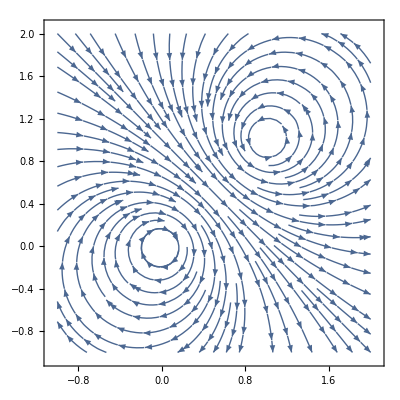

```mathematica
StreamPlot[{(y/(r1^2))-((y-1)/(r2^2)),(-x/(r1^2))+((x-1)/(r2^2))}
   /.r1->{((x)^2+(y)^2)^0.5}/.r2->{((x-1)^2+(y-1)^2)^0.5},
    {x,-1,2},{y,-1,2},RegionFunction->Function[{x,y},((x^2)+((y)^2))≥0.01
&&((x-1)^2)+((y-1)^2)≥0.01]]
```

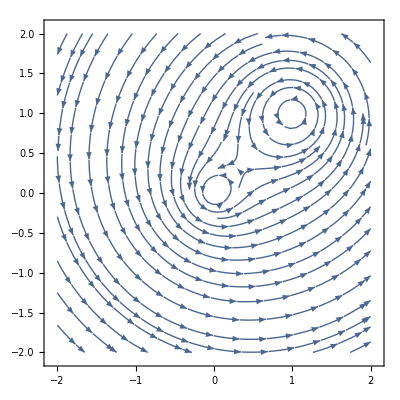

```mathematica
StreamPlot[{(-y/(2 (r1)^2))-((y-1)/(r2^2)),(x/(2(r1)^2))+((x-1)/(r2^2))}
/.r1->{((x)^2+(y)^2)^0.5}/.r2->{((x-1)^2+(y-1)^2)^0.5},
{x,-2,2},{y,-2,2}]
```

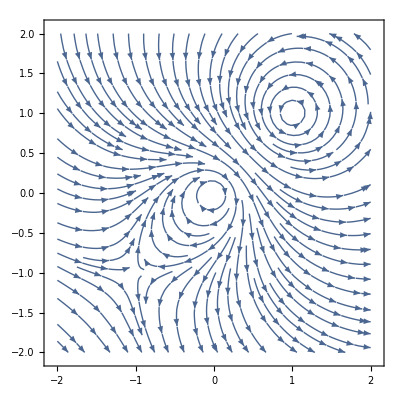

```mathematica
StreamPlot[{(y/(2(r1)^2))-((y-1)/(r2^2)),(-x/(2(r1)^2))+((x-1)/(r2^2))}
   /.r1->{((x)^2+(y)^2)^0.5}/.r2->{((x-1)^2+(y-1)^2)^0.5},
    {x,-2,2},{y,-2,2}]
```

# Using NDSolve

```mathematica
numsol = NDSolve[{x''[t]==-x[t]+(((x[t])^3)/6),x[0]==π/2,x'[0]==0},x[t],{t,0,10π}]
```

{{x[t]→InterpolatingFunction[…][t]}}

```mathematica
k[t_]=x[t]/.numsol
```

{InterpolatingFunction[…][t]}

```mathematica
Plot[{k[t],0.5 Cos[t]},{t,0,10π}]
```

-Graphics-

```mathematica
numsol1 = NDSolve[{x''[t]==-x[t],x[0]==π/2,x'[0]==0},x[t],{t,0,10π}]
```

{{x[t]→InterpolatingFunction[…][t]}}

```mathematica
k1[t_]=x[t]/.numsol1
```

{InterpolatingFunction[…][t]}

```mathematica
Plot[{k[t],k1[t]},{t,0,10π}]
```

-Graphics-

# Fibonacci Numbers

```mathematica
For[mylist={0,1},Length[mylist]≤10,AppendTo[mylist,mylist⟦-1⟧+mylist⟦-2⟧]]
mylist
```

{0,1,1,2,3,5,8,13,21,34,55}

# Stirling's Approximation

```mathematica
t1 =Sum[1/(n^(5/2))//N,{n,1,19}]
t2 = Table[(n Log[n])-n,{n,1,10}];
t3 = Table[(n Log[n])-n+((1/2)(Log[2π n])),{n,1,10}];
```

1.33375

```mathematica
9
```

# The Euler Function

```mathematica
ti=0;
tf=5;
nMax=1000;
h=(tf-ti)/nMax;
datalist={{ti,1}};
f[x_,t_]=-2.0t;

For[ctr=0,ctr≤nMax,ctr++,
tPrev=ti+h(ctr-1);
xPrev=datalist⟦-1,2⟧;
tNext=tPrev+h;
xNext=xPrev+h f[xPrev,tPrev];
AppendTo[datalist,{tNext,xNext}];
]
(*x[t1_]=NIntegrate[function,{0,t,t1}]*)

plot1=Plot[{1-(t^2)},{t,0,5}];
plot2=ListPlot[datalist];
Show[plot1,plot2]
```

-Graphics-

# Module for Euler Function

```mathematica
Euler[func_,xi_,ti_,tf_,nMax_]:=Module[{h,datalist,prev},
h=(tf-ti)/nMax//N;
For[
datalist={{ti,0}},
Length[datalist]≤nMax,
AppendTo[datalist,prev+{h,h f@@prev}],
prev=Last[datalist]
    ];
 Return[datalist]]
```

```mathematica
f[t_,x_]=1-t;
Euler[f,0,0,1,100]
```

{{0,0},{0.01,0.01},{0.02,0.0199},{0.03,0.0297},{0.04,0.0394},{0.05,0.049},{0.06,0.0585},{0.07,0.0679},{0.08,0.0772},{0.09,0.0864},{0.1,0.0955},{0.11,0.1045},{0.12,0.1134},{0.13,0.1222},{0.14,0.1309},{0.15,0.1395},{0.16,0.148},{0.17,0.1564},{0.18,0.1647},{0.19,0.1729},{0.2,0.181},{0.21,0.189},{0.22,0.1969},{0.23,0.2047},{0.24,0.2124},{0.25,0.22},{0.26,0.2275},{0.27,0.2349},{0.28,0.2422},{0.29,0.2494},{0.3,0.2565},{0.31,0.2635},{0.32,0.2704},{0.33,0.2772},{0.34,0.2839},{0.35,0.2905},{0.36,0.297},{0.37,0.3034},{0.38,0.3097},{0.39,0.3159},{0.4,0.322},{0.41,0.328},{0.42,0.3339},{0.43,0.3397},{0.44,0.3454},{0.45,0.351},{0.46,0.3565},{0.47,0.3619},{0.48,0.3672},{0.49,0.3724},{0.5,0.3775},{0.51,0.3825},{0.52,0.3874},{0.53,0.3922},{0.54,0.3969},{0.55,0.4015},{0.56,0.406},{0.57,0.4104},{0.58,0.4147},{0.59,0.4189},{0.6,0.423},{0.61,0.427},{0.62,0.4309},{0.63,0.4347},{0.64,0.4384},{0.65,0.442},{0.66,0.4455},{0.67,0.4489},{0.68,0.4522},{0.69,0.4554},{0.7,0.4585},{0.71,0.4615},{0.72,0.4644},{0.73,0.4672},{0.74,0.4699},{0.75,0.4725},{0.76,0.475},{0.77,0.4774},{0.78,0.4797},{0.79,0.4819},{0.8,0.484},{0.81,0.486},{0.82,0.4879},{0.83,0.4897},{0.84,0.4914},{0.85,0.493},{0.86,0.4945},{0.87,0.4959},{0.88,0.4972},{0.89,0.4984},{0.9,0.4995},{0.91,0.5005},{0.92,0.5014},{0.93,0.5022},{0.94,0.5029},{0.95,0.5035},{0.96,0.504},{0.97,0.5044},{0.98,0.5047},{0.99,0.5049},{1.,0.505}}

0.

0.

0.

# Accuracy Test for Euler's Method

```mathematica
err[dataset_,solution_]:=Module[{xlist,tlist,sollist},
tlist=dataset⟦2;;,1⟧;
xlist=dataset⟦2;;,2⟧;
sollist=solution/@tlist;
Return[xlist-sollist//Abs//N//Mean];
]
```

```mathematica
sol[t_]=t-0.5*(t^2);
err[Euler[f,1,0,5,1000],sol]*1000
```

6.25625